```mathematica
ariasD[0] = 1;
ariasD[n_Integer?Positive] := ariasD[n] = Sum[2^((k (k - 1) - n (n - 1))/2) ariasD[k]/(n - k + 1)!, {k, 0, n - 1}]/(2^n - 1);
iFabiusF[x_]:=Module[{prec=Precision[x],n,p,q,s,tol,w,y,z},If[x<0,Return[0,Module]];tol=10^(-prec);
z=SetPrecision[x,Infinity];s=1;y=0;
z=If[0≤z≤2,1-Abs[1-z],q=Quotient[z,2];
If[ThueMorse[q]==1,s=-1];
1-Abs[1-z+2 q]];
While[z>0,n=-Floor[RealExponent[z,2]];p=2^n;
z-=1/p;w=1;
Do[w=ariasD[m]+p z w/(n-m+1);p/=2,{m,n}];
y=w-y;
If[Abs[w]<Abs[y] tol,Break[]]];
SetPrecision[s Abs[y],prec]];
FabiusF[Infinity] = Interval[{-1, 1}];
FabiusF[x_?NumberQ] /; If[Im[x] == 0, TrueQ[Composition[BitAnd[#, # - 1] &, Denominator][x] == 0], False] := iFabiusF[x];
Derivative[n_Integer][FabiusF] := 2^(n (n + 1)/2) FabiusF[2^n #] &;
SetAttributes[FabiusF, {NumericFunction, Listable}];//Timing//AbsoluteTiming
```

{0.0000134748,{0.,Null}}

```mathematica
ClearAll[iCurvaturePlotHelper, CurvaturePlot]
iCurvaturePlotHelper[f_?(Head[#] =!= List &), {t_, tmin_, tmax_}, {{x0_, y0_}, θ0_}, opts : OptionsPattern[]] := Module[{sol, θ, x, y, if},
  sol = NDSolve[{
     θ'[t] == f,
     x'[t] == Cos[θ[t]],
     y'[t] == Sin[θ[t]],
     θ[tmin] == θ0,
     x[tmin] == x0,
     y[tmin] == y0
     }, {x, y}, {t, tmin, tmax}, opts];
  if = {x[#], y[#]} & /. First[sol];
  if]
CurvaturePlot[f_, {t_, tmin_, tmax_}, opts : OptionsPattern[]] := CurvaturePlot[f, {t, tmin, tmax}, {{0, 0}, 0}, opts]
CurvaturePlot[f_, {t_, tmin_, tmax_}, p : {{x0_, y0_}, θ0_}, opts : OptionsPattern[]] := Module[{θ, x, y, sol, rlsplot, rlsndsolve, if, ifs},
  rlsplot = FilterRules[{opts}, Options[ParametricPlot]];rlsndsolve = FilterRules[{opts}, Options[NDSolve]];
  If[Head[f] === List,
   ifs = iCurvaturePlotHelper[#, {t, tmin, tmax}, p, Evaluate@(Sequence @@ rlsndsolve)] & /@ f;
   ParametricPlot[Evaluate[#[tplot] & /@ ifs], {tplot, tmin, tmax}, Evaluate@(Sequence @@ rlsplot)]
   ,
   if = iCurvaturePlotHelper[f, {t, tmin, tmax}, p, Evaluate@(Sequence @@ rlsndsolve)];
   ParametricPlot[Evaluate[if[tplot]], {tplot, tmin, tmax}, Evaluate@(Sequence @@ rlsplot)]
   ]];//Timing//AbsoluteTiming
```

{0.0000682926,{0.,Null}}

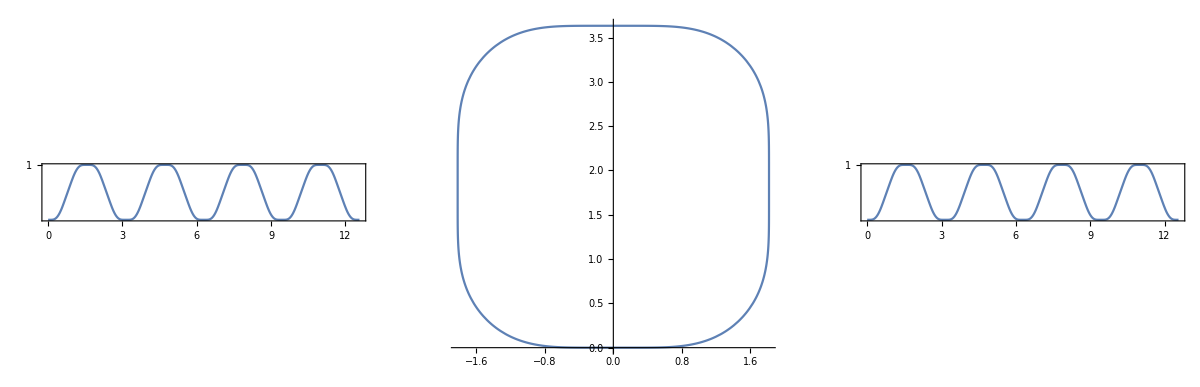

```mathematica
⚪ᔓᔕ⚪ᑎ⚪ꖴ⚪8⚪ᗩ⚪ꗳ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ꗳ⚪ᗩ⚪8⚪ꖴ⚪ᑎ⚪ᔓᔕ⚪ = Abs[FabiusF[X/π*2]];
GraphicsGrid[
{
{
Plot[⚪ᔓᔕ⚪ᑎ⚪ꖴ⚪8⚪ᗩ⚪ꗳ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ꗳ⚪ᗩ⚪8⚪ꖴ⚪ᑎ⚪ᔓᔕ⚪,{X,0,4π},Axes->True,AspectRatio->.5/π,Frame->True,FrameTicks->{Automatic,{1}},ImageSize->Full],
CurvaturePlot[⚪ᔓᔕ⚪ᑎ⚪ꖴ⚪8⚪ᗩ⚪ꗳ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ꗳ⚪ᗩ⚪8⚪ꖴ⚪ᑎ⚪ᔓᔕ⚪,{X,0,4 π}, Axes -> {False,True},ImageSize->Full],
Plot[⚪ᔓᔕ⚪ᑎ⚪ꖴ⚪8⚪ᗩ⚪ꗳ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ꗳ⚪ᗩ⚪8⚪ꖴ⚪ᑎ⚪ᔓᔕ⚪,{X,0,4 π},Axes->True,AspectRatio->.5/π,Frame->True,FrameTicks->{Automatic,{1}},ImageSize->Full]
}
},
ImageSize->Full
]
```

```mathematica
Plot3D[FabiusF[1-x]*FabiusF[1-y],{x,-1,1},{y,-1,1},ColorFunction->Function[{x,y,z},Glow[GrayLevel[z]]],PlotRange->All,Mesh->None,AspectRatio->1,Lighting->None,ViewPoint->{0,0,Infinity},ImageSize->Large,Boxed->False,Axes->False,PlotPoints->17,BoundaryStyle->None]
```

-Graphics3D-

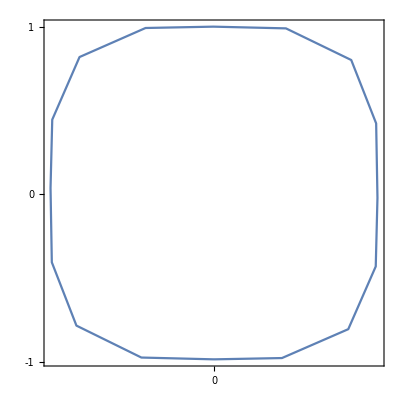

Show[{{6.514233596988106000935658812522888183594×10^-14,-0.9832446820137723531018991707242093980312},{0.1030581095920683615263513388526916969568,-0.9755609113566676704465407965471968054771},{0.203629433032755990939932644323562271893,-0.8034059268584972102189567522145807743073},{0.2453030298200142844677884568227455019951,-0.429473644509418939207989751594141125679},{0.2479055852472178966827698332053842023015,-0.02051466102835708404938941384898498654366},{0.2459207564880950824814931365835946053267,0.4232696545548655375768021258409135043621},{0.2081347206034768748672547644673613831401,0.8011186257003934940712497336789965629578},{0.1090961226020837199213175949807919096202,0.9897624221555094692348575335927307605743},{-0.001037186239265366904938048264739336445928,1.},{-0.1037931845752375764613262276725436095148,0.9920333523519193619222278357483446598053},{-0.2039387785249806017695561877189902588725,0.8189110472402330032082318211905658245087},{-0.2453195767620130474107043028197949752212,0.4456687184425458525538488174788653850555},{-0.2479055852460438358342287301638862118125,0.03790070699377934282381374941905960440636},{-0.2459645722279324986381254802836338058114,-0.4046971729130425243781132849107962101698},{-0.208638884362444598785657490225275978446,-0.7821146893214185880083277879748493432999},{-0.1101425680894061176484655106833088211715,-0.9725088723843444693528681455063633620739},{5.354050536254817416192963719367980957031×10^-14,-0.9832446820140328114234762324485927820206}}]

```mathematica
⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪=CurvaturePlot[Evaluate[SetPrecision[SetAccuracy[⚪ᔓᔕ⚪ᑎ⚪ꖴ⚪8⚪ᗩ⚪ꗳ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ꗳ⚪ᗩ⚪8⚪ꖴ⚪ᑎ⚪ᔓᔕ⚪,Infinity],Infinity],{X,0,4π},WorkingPrecision->30,Accuracy->Infinity,MaxRecursion->0,PlotPoints->17], Axes -> {True,True}]/. {X_Real,Y_Real}:>{Evaluate[SetPrecision[SetAccuracy[Rescale[X,Last@PlotRange@⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪,{0,1}],40],40]],Evaluate[SetPrecision[SetAccuracy[Rescale[Y,Last@PlotRange@⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪,{-1,1}],40],40]]};
Show[⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪,Frame->True,FrameTicks->{{-1,0,1}, {-1,0,1}},PlotRange->Full,AspectRatio->1]/. {X_Real,Y_Real}:>{Evaluate[SetPrecision[SetAccuracy[Rescale[X,Last@PlotRange@⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪,{0,1}],40],40]],Evaluate[SetPrecision[SetAccuracy[Rescale[Y,Last@PlotRange@⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪,{-1,1}],40],40]]}
⚪ᗩ⚪✤⚪ᗩ⚪ᗝ⚪◯⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪◯⚪ᗝ⚪ᗩ⚪✤⚪ᗩ⚪=Flatten[Cases[⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪,Line[X__]->X,Infinity],1]/. {X_Real,Y_Real}:>{Evaluate[SetPrecision[SetAccuracy[Rescale[X,Last@PlotRange@⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪,{0,1}],40],40]],Evaluate[SetPrecision[SetAccuracy[Rescale[Y,Last@PlotRange@⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪,{-1,1}],40],40]]};
Export["⚪ᗩ⚪✤⚪ᗩ⚪ᗝ⚪◯⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪◯⚪ᗝ⚪ᗩ⚪✤⚪ᗩ⚪",⚪ᗩ⚪✤⚪ᗩ⚪ᗝ⚪◯⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪◯⚪ᗝ⚪ᗩ⚪✤⚪ᗩ⚪,"CSV"];
Show[⚪ᗩ⚪✤⚪ᗩ⚪ᗝ⚪◯⚪✤⚪Ⓞ⚪ᙁ⚪ߦ⚪◌⚪◌⚪◌⚪◌⚪◌⚪◌⚪ߦ⚪ᙁ⚪Ⓞ⚪✤⚪◯⚪ᗝ⚪ᗩ⚪✤⚪ᗩ⚪]
```